# How to make standing variation

## distribution of s from new mutation

In FGM the PDF of selective effects of new mutations relative to the wildtype, s = logW-logW_wt, is (Martin & Lenormand 2015)

```mathematica
fs[s_,so_,λ_,n_]:=2/λ PDF[NoncentralChiSquareDistribution[n,(2so)/λ],2/λ(so-s)]HeavisideTheta[so-s];
```

This assumes a multivariate normal mutational distribution with no covariance (isotropy) and a symmetric Gaussian fitness landscape W.

In our case we are interested in a wildtype at the optimum, so=0

```mathematica
fs[s_,λ_,n_]:=Simplify[fs[s,0,λ,n],{s<0,λ>0}]
```

The remaining parameters are the mutational variance λ and the dimensionality of the landscape n. Note that we could alternatively use parameters n and Es, the expected selection coefficient against a mutation, by setting λ = 2 Es / n

-(2^(-n/2) ⅇ^((n s)/(2 Es)) (-(n s)/Es)^(n/2))/(s Gamma[n/2])

-Es

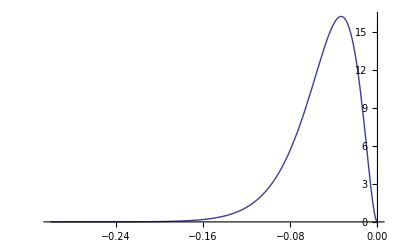

```mathematica
fs[s,λ,n]/.λ->2Es/n
Integrate[s%,{s,-∞,0},Assumptions->{Es>0,n>0}]
Plot[%%/.Es->0.05/.n->6,{s,-0.3,0},PlotRange->All]
```

Note that in two dimensions this is particularly simple

ⅇ^(s/Es)/Es

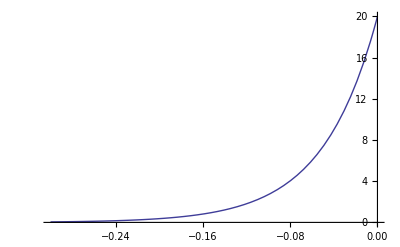

```mathematica
fs[s,λ,n]/.λ->2Es/n/.n->2
Plot[%/.Es->0.05,{s,-0.3,0},PlotRange->All]
```

ie -s is exponentially distributed with mean -Es

```mathematica
PDF[ExponentialDistribution[1/Es],-s]
Expectation[-s,s\[Distributed]ExponentialDistribution[1/Es]]
```

Piecewise[{{ⅇ^(s/Es)/Es, -s≥0}, {0, True}}]

-Es

## segregation times

For a continuous-time birth (λ) death (μ) process starting from N0 individuals (F[s,0]==s^N0) the PGF for the PDF of the number of individuals at time t can be solved for explicitly

```mathematica
fst=DSolve[{D[F[s,t],t]==D[F[s,t],s](λ s^2-(λ+μ)s+μ),F[s,0]==s^N0},F[s,t],{s,t}]//Flatten
```

{F[s,t]→((ⅇ^((μ (t λ-t μ+Log[-1+s]-Log[s λ-μ]))/(λ-μ))-ⅇ^((λ (t λ-t μ+Log[-1+s]-Log[s λ-μ]))/(λ-μ)) μ)/(ⅇ^((μ (t λ-t μ+Log[-1+s]-Log[s λ-μ]))/(λ-μ))-ⅇ^((λ (t λ-t μ+Log[-1+s]-Log[s λ-μ]))/(λ-μ)) λ))^N0}

Giving probability of extinction at time t

```mathematica
pextt=F[s,t]/.fst/.s->0//Factor//Simplify//FullSimplify
```

(1+(-λ+μ)/(λ-ⅇ^(t (-λ+μ)) μ))^N0

Evaluating at s=0 as t goes to infinity gives the probabilty the lineage ever goes extinct. When birth rate is greater than death rate we have

```mathematica
pextinction=Limit[F[s,t]/.fst/.s->0,t->∞,Assumptions->{λ>μ,μ>0}]
```

(μ/λ)^N0

and when death rate is greater than birth rate we have

```mathematica
Limit[F[s,t]/.fst/.s->0,t->∞,Assumptions->{λ<μ,μ>0}]
```

1

The probability of persistence to time t is just one minus the probability of extinction by time t

```mathematica
pest=1-pextt
```

1-(1+(-λ+μ)/(λ-ⅇ^(t (-λ+μ)) μ))^N0

From here on will we follow Uecker and Hermisson and let λ→(1+s)/2,μ→(1-s)/2 so that the continuous time branching process results match discrete time recursion equations.

We then get a probability of establishment that matches Haldane when s is small

```mathematica
1-pextinction/.λ->(1+s)/2/.μ->(1-s)/2/.N0->1;
Series[%,{s,0,1}]//Normal
```

2 s

When |1/s| << 1/t << 1 (that is, at late times but while the mutant is still effectively neutral) the probability that a new mutant lineage persists to time t is approximately

```mathematica
pestapp1=Normal[Series[pest/.λ->(1+s)/2/.μ->(1-s)/2/.N0->1/.s ->s ϵ^2/.t->t /ϵ,{ϵ,0,1}]]/.ϵ->1
```

2/t

And when -s t >>1, ie -s >> 1/t (that is, when the mutant is effectively deleterious) we have

```mathematica
pestapp2=Simplify[pest/.λ->(1+s)/2/.μ->(1-s)/2/.N0->1]/. 1+ⅇ^(-s t) (-1+s)+s->ⅇ^(-s t) (-1+s)
```

(2 ⅇ^(s t) s)/(-1+s)

Visually check the small t (red) and large t (green) approximations of the full solution (blue)

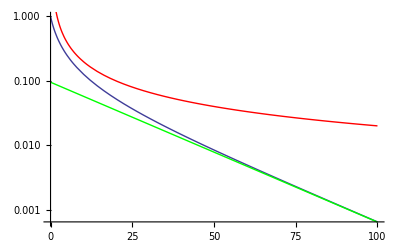

```mathematica
Show[
LogPlot[pest/.λ->(1+s)/2/.μ->(1-s)/2/.N0->1/.s->-0.05,{t,0,100}],
LogPlot[pestapp1/.s->-0.05,{t,0,100},PlotRange->All,PlotStyle->Red],
LogPlot[pestapp2/.s->-0.05,{t,0,100},PlotRange->All,PlotStyle->Green]
]
```

When the mutation is weakly deleterious, -s<<1, but we look at late times so that 1/t << -s (together giving 1/t << -s << 1), the distribution of persistence times is exponential with parameter -s, giving mean persistence time -1/s

```mathematica
pestapp2/.-1+s->-1;
Integrate[%,{t,0,∞},Assumptions->s<0];
%%/%
%==Simplify[PDF[ExponentialDistribution[-s],t],t>0]
Expectation[t,t\[Distributed]ExponentialDistribution[-s]]
```

-ⅇ^(s t) s

True

-1/s

## probability mutation with effect s is segregating

Mutations that segregate longer are more likely to be in the standing genetic variation at any given time, given they appear. Here we use this logic to get the PDF of s in the standing variation:
f(s | segregating) = (Pr(segregating | s) f(s))/(∫Pr(segregating | s) f(s)ds). 

We will assume the probability of segregating given s is proportional to the expected segregation time given such a mutation arises, -1/s, as shown above. We then have, for n>2,

```mathematica
-1/s fs[s,λ,n];
Integrate[%,{s,-∞,0},Assumptions->{λ>0,n>2}];
%%/%
```

(ⅇ^(s/λ) (-2+n) (-s/λ)^(n/2) λ)/(2 s^2 Gamma[n/2])

This moves the distribution of s to smaller values:

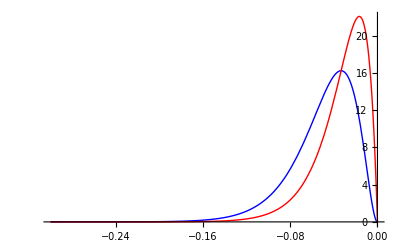

```mathematica
Show[
Plot[fs[s,λ,n]/.λ->2Es/n/.Es->0.05/.n->6,{s,-0.3,0},PlotStyle->Blue],
Plot[(ⅇ^(s/λ) (-2+n) (-s/λ)^(n/2) λ)/(2 s^2 Gamma[n/2])/.λ->2Es/n/.Es->0.05/.n->6,{s,-0.3,0},PlotStyle->Red],
PlotRange->All
]
```

When n≤2 the integral does not converge with small s and we are forced to approximate by integrating up to neutral mutations (-s<1/Ne, where Ne is the effective population size)

```mathematica
-1/s fs[s,λ,2];
Integrate[%,{s,-∞,-1/Ne},Assumptions->{λ>0,n<3,Ne>1}];
Simplify[%%/%,{s<0,λ>0,Ne>1}]
```

-ⅇ^(s/λ)/(s Gamma[0,1/(Ne λ)])

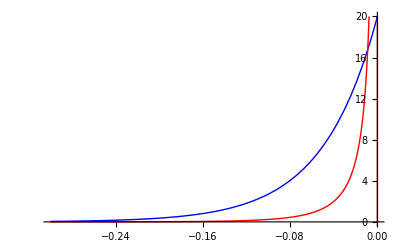

```mathematica
Show[
Plot[fs[s,λ,n]/.λ->2Es/n/.Es->0.05/.n->2,{s,-0.3,0},PlotStyle->Blue],
Plot[-ⅇ^(s/λ)/(s Gamma[0,1/(Ne λ)])/.λ->2Es/n/.Es->0.05/.n->2/.Ne->10^4,{s,-0.3,1/10^4},PlotStyle->Red,PlotRange->{0,20}],
PlotRange->All
]
```

## distribution of mutation frequency given segregating

The probability that there is 1 individual at time t is

```mathematica
pn1=D[F[s,t]/.fst,{s,n}]/n!/.n->1/.s->0/.λ->(1+r)/2/.μ->(1-r)/2/.N0->1//Simplify
```

(4 ⅇ^(r t) r^2)/((-1+r+ⅇ^(r t) (1+r))^2)

and two individuals

```mathematica
pn2=D[F[s,t]/.fst,{s,n}]/n!/.n->2/.s->0/.λ->(1+r)/2/.μ->(1-r)/2/.N0->1//Simplify
```

(4 ⅇ^(r t) (-1+ⅇ^(r t)) r^2 (1+r))/((-1+r+ⅇ^(r t) (1+r))^3)

three

```mathematica
D[F[s,t]/.fst,{s,n}]/n!/.n->3/.s->0/.λ->(1+r)/2/.μ->(1-r)/2/.N0->1//Simplify
```

(4 ⅇ^(r t) (-1+ⅇ^(r t))^2 r^2 (1+r)^2)/((-1+r+ⅇ^(r t) (1+r))^4)

From this series we can see that we can write the probability of n individuals at time t like

```mathematica
pnt=pn1(pn2/pn1)^(n-1);
```

Check:

```mathematica
pnt/(D[F[s,t]/.fst,{s,n}]/n!)/.n->3/.s->0/.λ->(1+r)/2/.μ->(1-r)/2/.N0->1//Simplify
```

1

And dividing by the probability of survival to time t gives the conditional probability of having n individuals at time t given a mutant lineage lives to time t

```mathematica
pntgt=pnt/pest/.λ->(1+r)/2/.μ->(1-r)/2/.N0->1/.r->s//FullSimplify
```

(2 s (1-(2 s)/(-1+s+ⅇ^(s t) (1+s)))^n)/((-1+ⅇ^(s t)) (1+s))

When t << -1/s  (effectively neutral) this is approximately

```mathematica
pntgtapp1=Normal[Series[pntgt/.s-> s ϵ,{ϵ,0,0}]]/.ϵ->1//FullSimplify
```

2 t^(-1+n) (2+t)^-n

which for large t (ie very neutral mutants) is approximately

```mathematica
pntgtapp1/. 2+t->t
```

2/t

Or when -1/s << t (ie deleterious mutants) we have approximately

```mathematica
pntgtapp2=pntgt/.-1+s+ⅇ^(s t) (1+s)->-1+s/.-1+ⅇ^(s t)->-1//Simplify
```

-(2 s ((1+s)/(1-s))^n)/(1+s)

Visually check small t (red) and large t (green) approximations against full solution (blue)

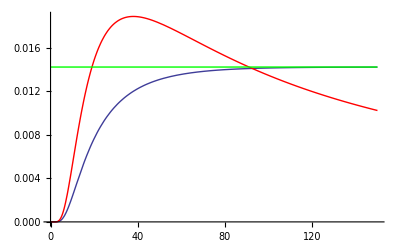

```mathematica
Show[
Plot[pntgt/.s->-0.05/.n->20,{t,0,150},PlotRange->All],
Plot[pntgtapp1/.s->-0.05/.n->20,{t,0,150},PlotRange->All,PlotStyle->Red],
Plot[pntgtapp2/.s->-0.05/.n->20,{t,0,150},PlotRange->All,PlotStyle->Green]
]
```

After long enough time all but wildtype mutations are effectviely deleterious (-1/s << t) and the PDF for the number of individuals in a lineage given it is segregating for a long time is

((1+s)/(1-s))^n Log[(1-s)/(1+s)]

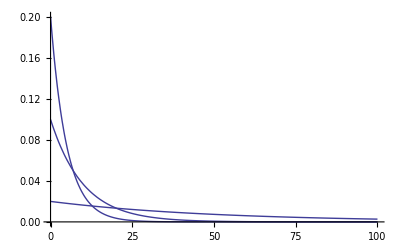

```mathematica
-(2 s ((1+s)/(1-s))^n)/(1+s);
Integrate[%,{n,0,∞},Assumptions->-1<s<0];
%%/%
Plot[%/.s->{-0.1,-0.05,-0.01},{n,0,100},PlotRange->All]
```

## converting s to a vector in phenotypic space

With a Gaussian fitness landscape with wildtype at the optimum, the selection coefficient of a mutation with phenotypic length r has selection coefficient

```mathematica
Simplify[Log[Exp[-r^2/2]]-Log[Exp[-0^2/2]],r>0]
```

-r^2/2

We can therefore solve for r

```mathematica
Simplify[Solve[s==-r^2/2,r][[1]],s<0]
```

{r→√2 √-s}

and with isotropic mutation we can uniformly choose a direction from the wildtype, meaning that we can place a mutation with effect s uniformly on the hypersphere with radius √(-2s).

For example, in 2-dimensional space we can choose a value in dimension 1 (x) uniformly between -√(-2s) and √(-2s). We then make the value in dimension 2 (y) equal to

```mathematica
Solve[x^2+y^2==r^2/.r->√2 √-s,y]
```

{{y→-√(-2 s-x^2)},{y→√(-2 s-x^2)}}

choosing the positive or negative with equal probability (Bernoulli with p=1/2).

## attempt to sample a mutation with n>2

With n>2 the PDF of s given segregation is

```mathematica
(ⅇ^(s/λ) (-2+n) (-s/λ)^(n/2) λ)/(2 s^2 Gamma[n/2]);
```

This gives CDF of the negative selection coefficient -s

1-Gamma[-1+n/2,x/λ]/Gamma[1/2 (-2+n)]

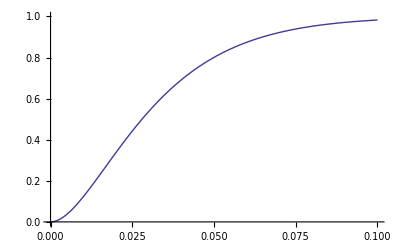

```mathematica
Integrate[(ⅇ^(s/λ) (-2+n) (-s/λ)^(n/2) λ)/(2 s^2 Gamma[n/2]),{s,-x,0},Assumptions->n>2]
Plot[%/.λ->2Es/n/.Es->0.05/.n->6,{x,0,0.1},PlotRange->{0,1}]
```

The inverse CDF is then

```mathematica
Solve[y==1-Gamma[-1+n/2,x/λ]/Gamma[1/2 (-2+n)],x]
```

Solve::nsmet: This system cannot be solved with the methods available to Solve.

Solve[y==1-Gamma[-1+n/2,x/λ]/Gamma[1/2 (-2+n)],x]

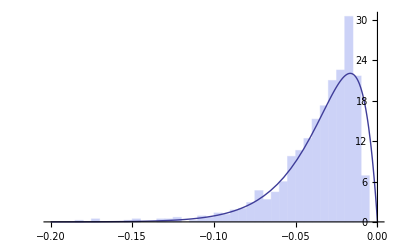

```mathematica
ntrials=1000;
Ne=10^4;
λ=2Es/n;
Es=0.05;
n=6;
rand1=RandomReal[1,ntrials];
Table[-x/.FindRoot[rand1[[i]]-(1-Gamma[-1+n/2,x/λ]/Gamma[1/2 (-2+n)]),{x,0.1}],{i,ntrials}];
Show[
Histogram[%,50,"PDF"],
Plot[(ⅇ^(s/λ) (-2+n) (-s/λ)^(n/2) λ)/(2 s^2 Gamma[n/2]),{s,-0.2,0},PlotRange->{0,200}],
PlotRange->{{-0.2,0},{0,All}},
AxesOrigin->{0,0}
]
Clear[Ne,λ,Es,n]
```

## attempt to sample a mutation with n>2

With n>2 the PDF of s given segregation is

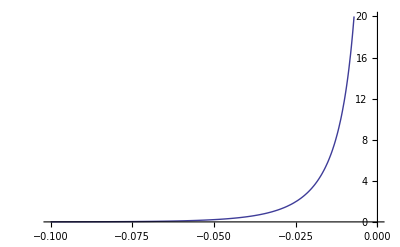

```mathematica
-ⅇ^(s/λ)/(s Gamma[0,1/(Ne λ)]);
Plot[%/.λ->2Es/n/.Es->0.05/.n->6/.Ne->10^4,{s,-0.1,0},PlotRange->{0,20}]
```

This gives CDF of the negative selection coefficient -s

(-ExpIntegralEi[-1/(Ne λ)]+ExpIntegralEi[-x/λ])/Gamma[0,1/(Ne λ)]

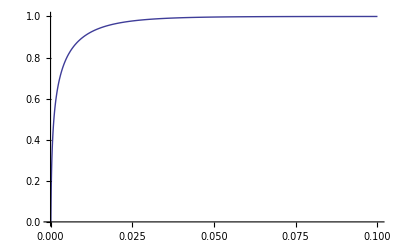

```mathematica
Integrate[-ⅇ^(s/λ)/(s Gamma[0,1/(Ne λ)]),{s,-x,-1/Ne},Assumptions->{n≤2,1/x>Ne>1}]
Plot[%/.λ->2Es/n/.Es->0.05/.n->6/.Ne->10^4,{x,0,0.1},PlotRange->{0,1}]
```

The inverse CDF is then

```mathematica
Solve[y==(-ExpIntegralEi[-1/(Ne λ)]+ExpIntegralEi[-x/λ])/Gamma[0,1/(Ne λ)],x]
```

Solve::nsmet: This system cannot be solved with the methods available to Solve.

Solve[y==(-ExpIntegralEi[-1/(Ne λ)]+ExpIntegralEi[-x/λ])/Gamma[0,1/(Ne λ)],x]

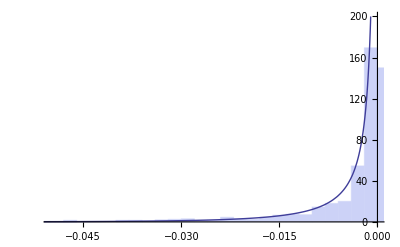

```mathematica
ntrials=1000;
Ne=10^4;
λ=2Es/n;
Es=0.05;
n=2;
rand1=RandomReal[1,ntrials];
Table[-x/.FindRoot[rand1[[i]]-(-ExpIntegralEi[-1/(Ne λ)]+ExpIntegralEi[-x/λ])/Gamma[0,1/(Ne λ)],{x,0.1}],{i,ntrials}];
Show[
Histogram[%,50,"PDF"],
Plot[-ⅇ^(s/λ)/(s Gamma[0,1/(Ne λ)]),{s,-0.1,0},PlotRange->{0,200}],
PlotRange->{{-0.05,0},{0,200}},
AxesOrigin->{0,0}
]
Clear[Ne,λ,Es,n]
```